# 第9章 程序设计

在上一章中，我们用形如￿f[x_]:= expr.94的 Mathematica 语句自定义一个函数。 该语句本质上是一个表达式。 Mathematica 的程序设计实际上也就是自定义函数的过程， 只不过是表达式的繁简程度有所不同而已。 一个表达式序列也称为一个复合表达式， 序列中各表达式用分号（；） 分隔。在 Mathematica 的各种语句中， 任何一个表达式的位置都能放一个复合表达式。 运行时按照顺序依次求各表达式的值， 并以最后一个表达式的值作为整个复
合表达式的值。 如果用一个复合表达式自定义一个函数， 要将这一串表达式用圆
括号括起来，最后一个表达式的值作为函数的值。

与一般结构化程序设计语言类似， Mathematica 提供了具有条件判断结构和
循环控制结构的语句，同时也保留了转向控制语句。

## 9.1 条件语句

在程序上和数学上， Mathematica 提供了 If、 Which 和 Switch 这 3 种条件语句。 
它们常用在程序设计中， 也可用于交互式行文命令中。

### 1. If语句

If[condition,t,f]    如果 condition 计算为 True 则给出 t，若计算为 False 则给出 f.

If[condition,t,f,u]   如果 condition 既不计算为 True 也不计算为 False 则给出 u.

```mathematica
abs[x_]:=If[x<0, -x, x]
```

```mathematica
Map[abs,{-2,0,5}]
```

{2,0,5}

```mathematica
f[x_,y_]:=If[x >0&&y >0, x +y, x -y]
```

```mathematica
f[4,-3]
```

7

```mathematica
f[2, u] (*无法判断真假*)
```

If[u>0,2+u,2-u]

```mathematica
f[x_,y_]:=If[x >0&&y >0, x +y, x -y, x y]
```

```mathematica
f[2,u]
```

2 u

例题：生成50个 [0,1]内随机数，判断该随机数是否小于0.5,如果小于 0.5,则将此随机数显示出来， 否则显示￿*￿

```mathematica
Table[If[(p = RandomReal[]) < 0.5, p, "*"], {n, 50}]
```

{0.173512,*,0.0954792,0.0212982,*,*,*,0.369359,*,0.122687,0.417692,*,*,0.367305,0.32456,0.260278,0.138779,0.240289,0.380305,*,0.329731,0.382978,0.0907542,0.462916,*,*,0.395768,*,*,0.105529,0.354068,*,0.0220628,*,0.329029,*,*,*,0.355366,*,*,0.051479,0.212389,0.357303,0.251289,0.239629,*,*,0.0260755,*}

例题：定义函数f(x)=Piecewise[{{x+Sin x, x<0}, {xSin x, 0≤x<2}, {xCos x, x≥2}}]并画出其在[-3,3]上的图形.

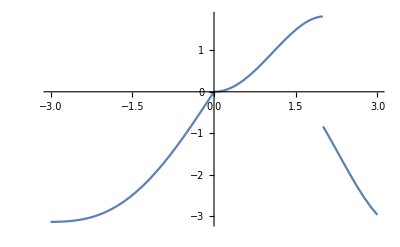

```mathematica
f[x_] := If[x < 0, x + Sin[x], If[x >= 2, x Cos[x], x Sin[x]]]

Plot[f[x], {x, -3, 3}]
```

### 2. Which 语句.

格式1：Which[条件1, 表达式1, 条件2, 表达式2,￿ 条件n, 表达式n,]	
功能:由条件 1 开始按顺序依次判断相应的条件是否成立， 若第一个成立的条件为条件k,则执行对应的表达式 k. 如所有条件都为假， 值为 Null， 作为整个结构的值

格式 2: Which[条件 1， 表达式 1，.85， 条件 n， 表达式 n， True, 表达式(n+1)]
功能:由条件 1 开始按顺序依次判断相应的条件是否成立， 若第一个成立的条件为条件k，则执行对应的 表达式k， 若直到条件 n 都不成立时，则返回表达式(n+1)

例题：定义分段函数 h(x)=-1 | x<-π/2
Sin x | -π/2≤x≤π/2
1 | x>π/2

```mathematica
h[x_]:= Which[x < -Pi/2, -1, x <= Pi/2, Sin[x], True, 1]
```

```mathematica
{h[-2], h[-1],h[0],h[1],h[2] , h[z]}
```

{-1,-Sin[1],0,Sin[1],1,Which[z<-π/2,-1,z≤π/2,Sin[z],True,1]}

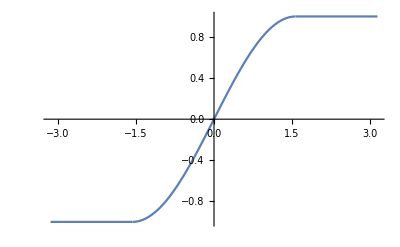

```mathematica
Plot[h[x],{x,-Pi,Pi}]
```

例题 定义函数 u(x)=Piecewise[{{-x, x<0}, {sinx, 0≤x<6}, {x/3
0, 16≤x<20
其他}}]，计算x=15,-12,5,18处的函数值.

```mathematica
u[x_]:=Which[x<0,-x,x<6,Sin[x],x<16,0,x<20,x/3,True,0]
{u[15],u[-12],u[5],u[18]}
u[x_]:=Which[x<0,-x,0<=x&&x<6,Sin[x], ,16<=x&&x<20,x/3,True,0]
```

{0,12,Sin[5],6}

例题：任给向量,定义一个可以计算下面三种矢量范数的函数

```mathematica
norm[x_,p_]:=Which[p==1,Sum[Abs[x][[i]],{i,1,Length[x]}], p==2, Sqrt[Sum[x[[i]]^2, {i,1,Length[x]}]], p==Infinity,Max[Abs[x]]]
Table[norm[{1, 2, 0, -5, 3}, p], {p, {1, 2, Infinity}}]
```

{11,√39,5}

### 3. Switch语句

Switch[表达式，模式 1,语句 1，模式2,语句2 模式 n,语句 n ]	
先计算表达式， 然后按模式 1 ,模式 2,…的顺序依次比较与表达式结果相同的模式， 找到的第一个相同的模式，则将此模式对应的语句计算计算结果作为 Switch 语句的结果.Switch 语句是根据表达式的执行结果来选择对应的执行语句， 它类似于一般计算机语言的Case 语句•

```mathematica
r[x_] := Switch[Mod[x, 3], 0, a, 1, b, 2, c]
r[4136]
```

c

### 4. 其他条件语句

Mathematica 中具有条件判断和分支选择结构的函数还有 Piecewise、 Cases、Count、 Position、Select 等

Piecewise[{{val1,cond1},{val2,cond2},...]
表示一个分段函数，在定义域内的条件 condi 值为 vali.

Piecewise[{{val1,cond1},...,val]
如果没有条件 condi，则取默认值 val. val 的默认值是 0.
condi 通常是不等式，比如, 依次判断条件 condi，直到其中的一个条件为 True.如果前面提到的所有条件 condi 都为 False，则把与第一个为 True 的条件 condi 相对应的值 vali，作为分段函数的函数值返回.

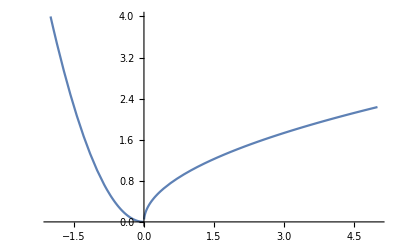

```mathematica
Plot[Piecewise[{{x^2,x<0},{x^(1/2), x>=0}}],{x,-2,5}]
```

```mathematica
D[Piecewise[{{x^2,x<0},{x^(1/2), x>=0}}],x]
```

Piecewise[{{2 x, x<0}, {1/(2 √x), x>0}, {Indeterminate, True}}]

利用 pw 来输入 { ，接着使用ctrl+,ctrl+Return 输入其他分支情况：

```mathematica
f[x_]:=Piecewise[{{Sin[x], 0<x<=Pi}, {2x-2Pi, Pi<x<2Pi}, {-x, x≤0}}]
```

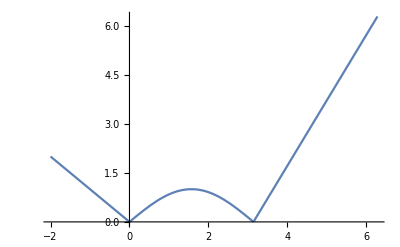

```mathematica
Plot[f[x],{x,-2,2Pi}]
```

## 9.2 循环语句

Mathematica 中有 3 种常用的循环语句，它们是 Do、 While 和 For 语句

### 1. Do语句

Do[expr,n]                      对 expr 计算 n 次.

Do[expr,{i,imax}]                 将变量 i 从 1 递增到 imax（步长为 1），计算 expr.

Do[expr,{i,imin,imax}]             从 i=imin 开始.

Do[expr,{i,imin,imax,di}]           使用步长 di.

Do[expr,{i,{i1,i2,...}]               使用列表中的值 i1、i2、￿

Do[expr,{i,imin,imax},{j,jmin,jmax},   对于每个 i，循环地根据不同的 j 等，计算 expr.

```mathematica
Do[Print[RandomInteger[10]],3]
Do[Print[{i,j}], {i,2},{j,2}] (*两重循环的次序*)
```

8

5

2

{1,1}

{1,2}

{2,1}

{2,2}

Do[expr,spec1,spec2] 实际上等价于 Do[Do[expr,spec2],spec1].

例题 找出 300 至 1000 之间同时能被 17 和 7 整除的自然数

```mathematica
Do[If[Mod[i, 17] == 0 && Mod[i, 7] == 0, Print[i]], {i, 300, 1000}]
```

357

476

595

714

833

952

例题 找出方程5 x^2+7y+z/4=150满足x+y+z<100的正整数解.

```mathematica
Do[z= 4 (150 - 5 x^2 - 7 y);  If[x+y+z<100&&z>0,   Print["x=", x, "  y=", y, "  z=", z]], {x, 1, 100}, {y, 1, 100}]
```

x=1  y=18  z=76

x=1  y=19  z=48

x=1  y=20  z=20

x=2  y=16  z=72

x=2  y=17  z=44

x=2  y=18  z=16

x=3  y=12  z=84

x=3  y=13  z=56

x=3  y=14  z=28

x=4  y=7  z=84

x=4  y=8  z=56

x=4  y=9  z=28

x=5  y=1  z=72

x=5  y=2  z=44

x=5  y=3  z=16

例题:用牛顿迭代法计算 √11

```mathematica
x = 5.0; Do[x = (x + 11/x)/2, 10]; x
```

3.31662

例题 数值排序（选择排序法）

```mathematica
list = RandomSample[Range[10], 10]
Do[If[list[[i]] > list[[j]], list[[{i, j}]] = list[[{j, i}]]], {i, Length[list]}, {j, i + 1, Length[list]}]; list
```

{10,2,6,8,7,9,4,1,3,5}

{1,2,3,4,5,6,7,8,9,10}

### 2. While 语句

While[test,body]若 test=True，运算循环体 body，直到 test=False退出循环.

例题：用割线法求解方程x^3 - 2 x^2 + 7 x + 4 = 0 的根,要求误差| x_k-x_(k- 1) |< 10^-12， 割线法的公式是 x_(k+1)=x_k-(f(x_k)(x_k-x_(k-1)))/(f(x_k)-f(x_(k-1))),    x_0=-1, x_1=1

```mathematica
f[x_]:=x^3-2x^2+7x+4;
x0=-1;x1=1;
While[Abs[x0-x1]>10^(-12),x2=x1-(x1-x0) f[x1]/(f[x1]-f[x0]);x0=x1;x1=x2]
N[x1,12]
```

-0.487120155928

### 3. For循环语句

For[start,test,incr,body]
以 start为初值，然后重复计算 body 和 incr，直到 test 不能给出 True.  incr为循环变量修正，body为循环体。
先计算初值，接下来计算的序列是 test、body、incr. 只要 test 失败立即退出 For 循环。在使用 For 语句编写程序的过程中， 一定要注意 For 语句的用法， Mathematica 中的 For 和 While 和 C 语言中的 For 和 While 的工作方式大致相同， 但逗号和分号的作用在 Mathematica 中和在 C 语言中正好相反，用逗号作为 For 的各个部分的分隔符，用分号作为程序各个部分的分隔符。

例如：求 1+2+…+100

```mathematica
For[ s =0;n =1, n <=100, n++,  s+=n];  s
```

5050

```mathematica
For[s =0;n =1, n <=100 ,n++; s+=n]; s (* 错误的程序 *)
```

5150

```mathematica
For[ s =0,n = 1, n <=100；n++, s+=n];s (* 错误的程序 *)
```

0

例题 编制 10 以内整数加法自测程序
用随机函数 Random[ Integer , {0, 10}] 产生[0 ,10] 内的任意两个整数 s 和 t, 屏幕提示算式 t + s = , 用户键入一个计算结果y, 如果结 果正确 , 显示“真棒！” , 否 则 显示“请再算一次” , 等 待重 新 输入 , 直到 结果正确 , 每次给出 10 个算式

```mathematica
For[i=1, i<=3, i++ , 
t = Random[Integer, {0, 10}]; s = Random[Integer, {0, 10}];
  Print[t, "+", s, "="];
 y = Input[]; While[y != t + s, Print[t, "+", s, "=", y, "请再算一次"];
  Print[t, "+", s, "="]; y = Input[]];
 Print[t, "+", s, "=", y, "真棒"]]
```

1+10=

1+10=11真棒

10+3=

10+3=13真棒

10+1=

10+1=11真棒

注意：While、For语句中没有隐含的局部变量。（while和for是真的会改变n）

```mathematica
n=100;For[n=E,n<=10,n+=Pi,Print[n]]; n
```

ⅇ

ⅇ+π

ⅇ+2 π

ⅇ+3 π

特殊赋值语句

语句说明x++, x--在使用 x 的数值后 x+1（x-1）赋值给x

++x,--x在使用 x 前将 x 增(减)1

x+=y, x-=y, (x=x+y,   x=x-y) ,    x*=y, x/=y   (X=x*y,   x=x/y)

例题：三角形的自相似

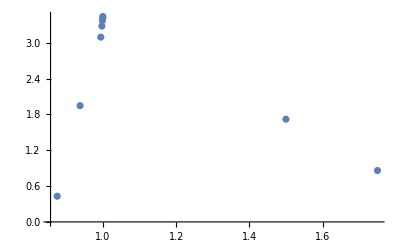

```mathematica
a[1]={0,0};
a[2]={2,0};
a[3]={1,2Sqrt[3]};
b[0]=Table[Random[Real,2],{2}];k=0;g[n_]:=Do[i=Random[Integer,{1,3}];b[k+1]=(b[k]+a[i])/2;k=k+1,{n}];n=Input[];
g[n];
x=Table[b[i],{i,2,n}];ListPlot[x]
```

## 9.3 转向语句

在自定义函数的时候， 经常会遇到需要提前结束程序并返回结果的情形;在设
计一些具有循环结构的运算的时候， 也经常会需要跳岀循环， 这时， 可以使
Mathematica 中的一些控制程序转向的语句。

函数                 说 明

Return[expr]结束程序运行， 返回结果 expr,expr 的缺省值为 Null(Do 里面的return不返回)

Break[]结束最内层的 Do,For.While 语句

Continue[ ]略过余下语句， 开始新一轮 Do、 For、 While 循环

Label[tag]Goto[tag]为 Goto 语句设置标号设下一语句入口为 tag

Throw[value],Catch[expr]    运算 expr，直到遇到 Throw[value]，然后返回 value1.

1. Return[expr] 退出一个函数定义内的控制结构，并给出整个函数的 expr 值, 但是仅退出调用它的最内层结构

```mathematica
f[x_] := (If[x > 5, Return[a]]; x)
g[x_] := (Do[If[x > 5, Return[a]], {3}];x)
```

```mathematica
{f[7],g[7]}
```

{a,7}

```mathematica
{f[3],g[3]}
```

{3,3}

2.  Break[ ]  退出最临近的内循环结构 Do、For 或 While.

```mathematica
Do[Print[i]; If[i > 2, Break[]], {i,0, 10}]
```

0

1

2

3

```mathematica
For[i = 1, i <= 10, i++, If[i > 2, Break[]]]; i
```

3

```mathematica
i = 1;
While[i <= 10, If[i > 2, Break[]]; i++]; i
```

3

3. Continue[ ]  退出一个过程式程序中的 Do，For 或 While 的最近封装.

```mathematica
t=1;
Do[t*=k;Print[t];If[k<3,Continue[]];t+=2,{k,5}]
```

1

2

6

32

170

```mathematica
For[i = 1, i <= 4, i++, If[i == 3, Continue[]]；Print[i]]
```

1

2

4

4. 利用 Label[ ]与 Goto[ ]语句， 可以实现在一个复合表达式内部的跳转

```mathematica
f[a_]:=Module[{x=1.0,xp},Label[begin]; If[Abs[xp-x]<10^(-8),Goto[end]];xp=x; x=(x+a/x)/2; Goto[begin];Label[end];x]
f[3]
```

1.73205

5. Throw 和 Catch 提供一种灵活的方式来控制 Wolfram 语言中的运算过程. 基本思想是，每当遇到一个 Throw 时，运算都将停止，并且 Wolfram 语言立即就近返回到适当的外层 Catch. 如果在运行时不生成 Throw，则 Catch[expr.85] 总是返回 expr 的值

```mathematica
Catch[Do[Print[i]; If[i !>4, Throw[i]], {i, 10}]]
```

1

2

3

3

找到列表中第一个负数

```mathematica
Catch[If[# < 0, Throw[#]] & /@ {3, -2, 0, -1, 5, 6}]
```

-2

```mathematica
f[x_] := Catch[
  Which[x <= 0, Throw["无定义"], True, 1/Sqrt[x]]]
{f[2], f[0],f[-2]}
```

{1/(√2),无定义,无定义}

## 9.4 程序模块

Mathematica 一般假设变量是全局变量.即每次使用 x 等名字时， Mathematica 总认为在调用同一对象，然而在编程时， 不需要将所有变量都作为全局变量.例如在两个不同的程序中， x 可用来指代两个不同的变量 .此时,每个程序中的 x 都必须作为局部变量. 

Mathematica 主要有以下几种程序模块。

(1)Module[{x,y,...},expr]   指定在 expr 中出现的符号 x、y、.85 应被当作局部值.

(2)Module[{x=x0,...},expr] 用来定义 x, .85 的初始值.

(3)DynamicModule[{x,y,...},expr]表示一个对象，可保持 expr 中所有Dynamic 对象在计算过程中符号 x、y、.85 的局部值. 在默认情况下， DynamicModule 中指定的符号甚至在整个 Mathematica 进程中都不会改变其值.

(4)DynamicModule[{x=x0,y=y0,...,expr]为 x、y、.85 指定初始值.

(5)Block[{x,y,...},expr]     指定用符号 x、y、.85 的局部值计算 expr.

(6)Block[{x=x0,...},expr]   给 x、 .85 赋初始局部值.

(7)With[{x=x0,y=y0,...},expr]指定expr中出现的符号 x,y,.85 应当由 x0,y0,.85 替换.

具体示例：
1.    Module

```mathematica
t=10;
Module[{t} , t= 8;Print[t]]
   t
```

8

10

t 在模块内， 所以它的处理与全局变量 t 无关全局变量 t 的值还是 10。
Mathematica 中模块的基本工作方式非常简单.任何模块每一次使用时， 就产生一个新符号去代表它的每一个局部变量.新符号的名字被唯一地给定， 它不能跟任何其它名字冲突.命名的方法是在给定的局部变量后加 $m ，m是唯一的序号。

```mathematica
Module[ {t} , Print[t]]
Module[{t , u} ,Print[t]; Print[ u]]
```

t$5979

t$5980

u$5980

```mathematica
t=10;
f[v_]:=Module[{t},t=(1+v)^2;t=Expand[t]]
f[a+b]
t
```

1+2 a+a^2+2 b+2 a b+b^2

10

在一个模块中定义局部变量时， Mathematica 开始并不对它赋值.即使在模块外定义了该变量的全局值,都能以纯符号的方式使用该变量.模块外部使用全局值.

```mathematica
Expand[(1+t)^3]
```

1331

对模块中任何一个变量都可以定义初始值， 这些初始值总是在模块执行之前进行计算 .即使定义了X 是模块的局部变量，在赋初始值时可以用全局变量的值(这里初始值有讲究)

```mathematica
Module[{t = 6, u = t},{t, u^2}]
```

{6,100}

在定义/;conditions 时经常需要引入临时变量，并且定义的右端也需要使用这些临时变量.Mathematica 允许将定义的右端和条件包含在模块之中.（先判断条件，故已经被赋值）

```mathematica
h[x_] := Module[{t}, Sin[t] - 1 /; (t = x - 4) > 1]
```

```mathematica
{h[2], h[2Pi]}
```

{h[2],-1-Sin[4]}

2.With 结构可以建立局部常数. 仅当它们在结构体中不作为局部变量出现时，With 替换 expr 中的符号.

```mathematica
w[x_]:=With[{t=x+1},t^3+2t+1]
w[a]
```

1+2 (1+a)+(1+a)^3

可以将 Module 和 With 混用.一般原则是某一变量最里面的 With 起作用.

```mathematica
Module[{t=8} ,With[{t = 9} ,2t]]
```

18

3. 在 Module[{ x} , body ] 中的变量 x 总是有一个唯一符号，模块每次调用时这符号不
同， 且与全局符号x 也有区别.Block[ { x }, body ] 中的 x 是一个全局的符号.这个块的作用是让x有局部值.进入这个块时x的值在退出该块时恢复， 而在块执行时， x 可以取任意值.

```mathematica
Clear[x,y,a]
```

```mathematica
x=15
Block[{x=a+1}, x^2+3]
```

15

3+(1+a)^2

```mathematica
m=i^2
Block[{i=a},i+m]
Module[{i=a},i+m]
```

25

25+a

25+a

Mathematics 的Block 可以暂时改变值的一种环境.在Block执行过程中用变量的当前值计算表达式，不论表达式是该Block语句中body的一部分或是在计算中某一处产生的情况都是如此. Block[ vars , body ] 不注意表达式 body 的形式， 而是在 body 的全局计算过程中使用的局部值.
ModuIe[ vars ,body ]的作用是在模块作为 Mathematica 的代码被执行时处理表达式 body 的形式，当任何明vars显地出现在代码中时， 就被当作局部变量

```mathematica
Clear[f,g,x,t]
```

```mathematica
f[x_]:=Block[{t},Integrate[Exp[x*t],{t,0,1}]] ;
g[x_]:=Module[{t},Integrate[Exp[x*t],{t,0,1}]];
```

```mathematica
{f[x],g[x],f[t],g[t]}
```

{(-1+ⅇ^x)/x,(-1+ⅇ^x)/x,1/2 √π Erfi[1],(-1+ⅇ^t)/t}

例题：绘制雪花曲线

```mathematica
snow[initial_List]:=Block[ {tmp={},i,L=Length[initial], sa=Sin[60Degree],ca=Cos[60Degree],T={{ca,-sa},{sa,ca}}},
For[i=1,   i<L, i++, 
c=initial[[i]]*2/3+initial[[i+1]]/3;
e=initial[[i]]/3+initial[[i+1]]*2/3;
d=c+T.(e-c);
tmp=Join[tmp,{initial[[i]],c,d,e,initial[[i+1]]}]];
Return[tmp]]
```

```mathematica
pt={{0,0},{1,0},{0.5,-Sqrt[3]/2},{0,0}};
```

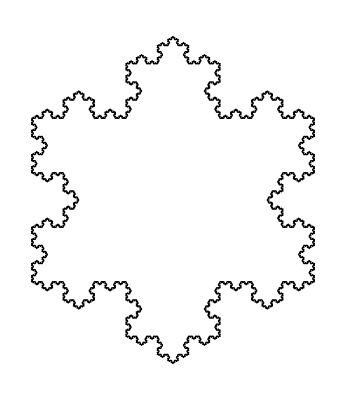

```mathematica
Show[Graphics[Line[Nest[snow,pt,5]]]]
```

例题：生成g (z) = z^2 +c对应的Julia, Mandelbrot分形图

序列z_n=(z_(n-1))^2+c， Julia集是使迭代 z = f(z)不收敛的初值 z。的集合。 从 z_0=0开始迭代，曼德尔布罗特集就是使序列不收敛的所有复数 c 的集合

```mathematica
g[z0_,c_]:=Module[{i=1,z=z0,w=z0^2+c},While[(++i)<50&&0.000001<Abs[w-z]<1000000,z=w;
w=z^2+c];i];
```

```mathematica
DensityPlot[g[x+y*I,-1.25],{x,-1,1},{y,-1,1},PlotPoints->100]
```

-Graphics-

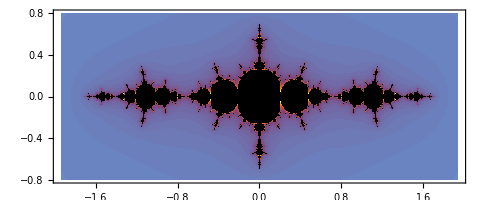

```mathematica
JuliaSetPlot[-1.25]
```

```mathematica
MandelbrotSetPlot[]
```

-Graphics-

```mathematica
MandelbrotSetPlot[{-0.65+0.47 I,-0.4+0.72 I},MaxIterations->200,ColorFunction->"RedBlueTones",PlotLegends->Automatic]
```

-Graphics-

## 9.5 程序调试

如果遇到 Mathematica 程序运行时间过长或陷入死循环， 则可以通过菜单项 Evaluation 或热键来暂停或终止程序的运行。点击菜单项计算—终止计算(Evaluation—Abort Evaluation)之后， 系统会退出全部表达式运算， 返回 $ Aborted。 点击菜单项.93 Evaluation-►Quit Kernel-►Local.94之后， 系统会结束 Mathematica 的后台内核程序。

点击菜单项￿，计算 —调试控制器(Evaulation —Debugger).94 可以供用户追踪程序之用。

除了使用菜单项之外，还可以插入调试的语句，常用的调试语句有

Abort[]终止程序运行， 返回 $ Aborted

Interrupt[]暂停程序运行，并弹出对话框

Exit或 Ouit[]结束 Mathematica 的后台内核程序

Check[expri ，expr2]先对 expn 求值，若捕捉异常信息， 再对 expr2求值

CheckAbort[expn ， expr2]先对 expr, 求值， 若捕捉 Abort， 再对 expr2求值

AbortProtect[expr]若捕捉 Abort， 在对 expr 求值完毕之后终止程序运

```mathematica
fpit[f_, start_, limit_] := FixedPoint[Function[{x}, If[Abs[x] > limit, Abort[], f[x]]], start, 10^6]
fpit[1 + 1/# &, 1., 100]
fpit[Exp, 1., 100]
```

1.61803

$Aborted

可以使用 Abort[ ] 在程序中实现.93紧急停止.94. 但在几乎所有情况下，都应尽量使用诸如 Return 和 Throw之类的函数，这些函数使行为受到更多控制.

如果中止发生在 Wolfram 语言表达式的运算过程中，Wolfram 语言通常会放弃对整个表达式的求值，并返回值 $Aborted.
但是，您可以使用函数 CheckAbort .93捕获.94中止行为. 如果在 CheckAbort[expr,failexpr] 中的 expr 运算期间发生中止，则 CheckAbort 返回 failexpr，但中止不会继续传播.

```mathematica
Clear[a,b,c,x]
```

```mathematica
CheckAbort[Abort[]; 1, 2] + x (*捕捉计算中某一部分的异常结束使其余的计算继续进行*)
CheckAbort[Print[a]; Abort[]; Print[b], Print[c]]
```

{{2.99401,5.095},{2.997,5.27955},{2.9985,5.37183},{2.99925,5.41796},{2.99963,5.44103},{3.49981,3.72052},{3.74991,2.86026},{2.87495,2.43013},{2.93748,3.94712}}

a

c

## 9.6 程序包

Wolfram 语言的一个重要特性在于其是一个可扩充系统. Wolfram 语言中已建立了一定数量的数学和其他功能. 然而，使用 Wolfram 语言，能添加更多的函数.
对许多种运算，Wolfram 语言标准版中建立的函数已经足够用了. 然而，当用户在一个特殊专业领域中讨论时，会需要使用特定函数，而这在 Wolfram 语言中是没有的.
在这种情况下，用户或许能在 Wolfram 语言程序包中找到所需的函数. Wolfram 语言程序包是用 Wolfram 语言写成的文件. 这些文件是由 Wolfram 语言定义集合组成，使 Wolfram 语言能进行特殊应用领域的工作.

程序包就是一些功能相近的函数和语句的集合， 按照某种方式组合在一起以便用户使用，相当于面向对象程序设计中的类. 当 Mathematica 启动的时候， 系统会自动加载一些软件包。 通过系统变量 $ Packages,我们可以知道哪些程序包已经被加载。通过系统变量 $ Path.我们可以知道这些程序包的位置。

```mathematica
$Packages
$Path
```

{CloudObject`,CloudObject`UserManagement`,MailReceiver`,Authentication`,Iconize`,Forms`,CloudObject`UsageData`,Interpreter`,GeneralUtilities`,Templating`,UUID`,CreateUUID`,Security`,DocumentationSearch`,EntityFramework`,CURLLink`URLResponseTime`,CURLLink`Utilities`,CURLInfo`,CURLLink`Cookies`,CURLLink`HTTP`,OAuthSigning`,CURLLink`URLFetch`,CURLLink`,Macros`,DocumentationSearch`Skeletonizer`,JLink`,GetFEKernelInit`,URLUtilities`,JSONTools`,PMCompatibility`,CloudObject`CreateUUID`,CloudObjectLoader`,ResourceFunctionHelpers`,CloudExpressionLoader`,NaturalLanguage`,NeuralNetworks`,UnitTable`,EntityFrameworkLoader`,WebAudioSearchLoader`,NeuralFunctions`,MobileMessaging`,IntegratedServices`,IconizeLoader`,HTTPHandling`,ExternalEvaluate`,Cryptography`,Blockchain`,AlphaScannerFunctions`,SystemTools`,SecureShellLink`,MailLinkLoader`,IMAPLinkLoader`,ResourceLocator`,PacletManager`,PersistenceLocations`,System`,Global`}

{C:\Users\86189\AppData\Roaming\Mathematica\DocumentationIndices,C:\Program Files\Wolfram Research\Mathematica\12.0\SystemFiles\Links,C:\Users\86189\AppData\Roaming\Mathematica\Kernel,C:\Users\86189\AppData\Roaming\Mathematica\Autoload,C:\Users\86189\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\86189,C:\Program Files\Wolfram Research\Mathematica\12.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\12.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\12.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\12.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\12.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\12.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\12.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\12.0\SystemFiles\Data\ICC}

当 Mathematica 刚被执行时， 有许多很专业化的函数和程序并没有被上载进系统.如果需
要它们的话,那就必须单独从 Mathematica 的硬盘目录中上载 .这些文件的形式为文件名.m
￿<<package             读入一个 Wolfram 语言程序包


程序包为纯文本格式， 通常后缀名.93 .m.94， 具有一般的形式为

```mathematica
BeginPackage[.93 程序包名.94 ]
f::=.93说明.94， ••• ( * 引入作为输出的目标 *)
Begin[.93Private.94]( * 开始程序包的私有上下文 *)
......( * 包的主体 *)
End[ ]  (* 结束自身的上下文 * )
EndPackage[ ] ( * 程序包结束标志，并将该程序包放到全局上下文路径的最前面 * )

程序包中的 f::usage 语句定义了函数 f 的使用信息，通常是对函数的描述和用法的说明.
```

```mathematica
BeginPackage["Mypackage"]
area::usage = "计算矩形的面积";
length::usage = "计算矩形周长";
area[x_, y_] := x *y 
length[x_, y_] := 2 *(x + y)
EndPackage[] :
 << Mypackage.m
```

BeginPackage::cxt: Invalid context specified at position 1 in BeginPackage[Mypackage]. A context must consist of valid symbol names separated by and ending with `.

BeginPackage[Mypackage]

Syntax::sntxf: "" cannot be followed by ""Mypackage"]".

Get::noopen: Cannot open Mypackage.m.

$Failed

例题：计算一组数据的算术平均值 、几何平均值 、中差、方差和标准差.

```mathematica
BeginPackage["Statistics"]
mean::usage="计算算术平均值";
geomean::usage="?计算几何平均值?";
median::usage="计算中位数";
var::usage="计算方差";
stdev::usage="计算标准差";
mean[x_]:=Total[x]/Length[x]
geomean[x_]:= Apply[Times,x]^(1/Length[x])
median[x_]:= Module[{n = Length[x],s =Sort[x]},
  If[OddQ[n],s[(n +1)/2],(s[[n/2]]+s[[n/2 +1]])/2]]
var[x_]:=mean[(x-mean[x])^2]
stdev[x_]:=Sqrt[var[x]]
EndPackage[ ]
```

BeginPackage::cxt: Invalid context specified at position 1 in BeginPackage[Statistics]. A context must consist of valid symbol names separated by and ending with `.

BeginPackage[Statistics]

EndPackage::noctx: No previous context defined.

EndPackage[]

将文件保存为"Statistics.m"

在新打开的.nb文件中输入
<< .94路径\ ￿即可使用包中的公共定义.私有定义仅在包内使用，不在外部公开.